# PDE Test Problems Van Der Vorst

## Reference

@article{doi:10.1137/0913035,
author = {van der Vorst, H. A.},
title = {Bi-CGSTAB: A Fast and Smoothly Converging Variant of Bi-CG for the Solution of Nonsymmetric Linear Systems},
journal = {SIAM Journal on Scientific and Statistical Computing},
volume = {13},
number = {2},
pages = {631-644},
year = {1992},
doi = {10.1137/0913035},
URL = {    https://doi.org/10.1137/0913035
},
eprint = {   https://doi.org/10.1137/0913035},
abstract = { Recently the Conjugate Gradients-Squared (CG-S) method has been proposed as an attractive variant of the Bi-Conjugate Gradients (Bi-CG) method. However, it has been observed that CG-S may lead to a rather irregular convergence behaviour, so that in some cases rounding errors can even result in severe cancellation effects in the solution. In this paper, another variant of Bi-CG is proposed which does not seem to suffer from these negative effects. Numerical experiments indicate also that the new variant, named Bi-CGSTAB, is often much more efficient than CG-S. }
}

## Test 1: -Δu=f on Ω=[0,1]^2 Homogeneous Dirichlet BC 150×150 grid

The points i=1:n  and j=1:n are all interior points. The fully interior points i=2:n-1 and i=2:n-1 use the standard five point stencil.  The boundary adjacent points i=1,n and j=1,n simply drop the coefficients associated with the boundary value that is zeroed by the homogeneous Dirichlet condition.

```mathematica
n=50;
Δx=Δy=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A1=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A1⟦k,k⟧=4.0;
If[1≤i+1≤n,A1⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A1⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A1⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A1⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A1
```

SparseArray[…]

## Test 2: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Mixed Neumann-Dirichlet Boundary Conditions

The plan is to build up to this slowly.  There are two new complications: boundary conditions and the function D.

### Test 1.8: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Neumann BC on y=0 and Dirichlet on the other three sides 150×150 grid With D=1.

The points i=1:n  and j=1:n are all interior points. The fully interior points i=2:n-1 and i=2:n-1 use the standard five point stencil.  The Dirichlet boundary adjacent points i=1,n and j=n simply drop the coefficients associated with the boundary value that is zeroed by the homogeneous Dirichlet condition.  The Neumann boundary adjacent points j=1 simply burn the (admittedly lower order) one sided difference implementation of the homogeneous Neumann condition 
	u_(i,0)=u_(i,1)
into the standard stencil 
	  |   | u_(i,2) |   |  
  |   | ↕ |   |  
u_(i-1,1) | ↔ | -4 u_(i,1) | ↔ | u_(i+1,1)
  |   | ↕ |   |  
  |   | u_(i,0) |   |  
to get
	  |   | u_(i,2) |   |  
  |   | ↕ |   |  
u_(i-1,1) | ↔ | -3 u_(i,1) | ↔ | u_(i+1,1)
  |   | ↕ |   |  
  |   | □ |   |  
This is relatively easy to implement

```mathematica
n=50;
Δx=Δy=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A18=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions *)
Do[
k=ijTok[n][i,j];
A18⟦k,k⟧=4.0;
If[1≤i+1≤n,A18⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A18⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A18⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A18⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,2,n}]
(* Neumann Condition *)
j=1;
Do[
k=ijTok[n][i,j];
A18⟦k,k⟧=3.0;
If[1≤i+1≤n,A18⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A18⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A18⟦k,ijTok[n][i,j+1]⟧=-1.0],
{i,1,n}
]
```

### Test 1.9: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Dirichlet Conditions on all sides

The key to thinking about the differencing for the non constant function is to just start making the recipe as before 
	(D(x,y)u_x)_x≈(D(x,y)((u(x+Δx/2,y)-u(x-Δx/2,y))/Δx))_x
and keep going
	(D(x,y)u_x)_x≈((D(x+Δx/2,y)((u(x+Δx/2+Δx/2,y)-u(x-Δx/2+Δx/2,y))/Δx)-D(x-Δx/2,y)((u(x+Δx/2-Δx/2,y)-u(x-Δx/2-Δx/2,y))/Δx))/Δx)
and then tidy up carefully
	(D(x,y)u_x)_x≈((D(x+Δx/2,y)((u(x+Δx,y)-u(x,y))/Δx)-D(x-Δx/2,y)((u(x,y)-u(x-Δx,y))/Δx))/Δx)
and then clean up the fractions 
	(D(x,y)u_x)_x≈(D(x+Δx/2,y)(u(x+Δx,y)-u(x,y))-D(x-Δx/2,y)(u(x,y)-u(x-Δx,y)))/Δx^2
and finally distribute the signs to get
	(D(x,y)u_x)_x≈(D(x+Δx/2,y)(u(x+Δx,y) - (D(x+Δx/2,y) + D(x-Δx/2,y))u(x,y) + D(x-Δx/2,y)u(x-Δx,y))/Δx^2.
The last step is to make some obvious definitions to help remember this 
	(D(x,y)u_x)_x|_(i,j)≈(D_(i+1/2,j)u_(i+1,j) - (D_(i+1/2,j) + D_(i-1/2,j))u_(i,j) + D_(i-1/2,j)u_(i-1,j))/Δx^2.
Not surprisingly, the y derivative version is 
	(D(x,y)u_y)_y|_(i,j)≈(D_(i,j+1/2)u_(i,j+1) - (D_(i,j+1/2) + D_(i,j-1/2))u_(i,j) + D_(i,j-1/2)u_(i,j-1))/Δy^2.	 
Adding the two together gives an approximation to the desired PDE.

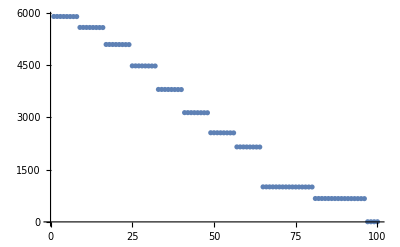

```mathematica
n=10;
Δx=Δy=1.0/(n+1);
DFun[x_,y_]:= If[And[0.1≤x≤0.9,0.1≤y≤0.9],1000.0,1.0]
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A19=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions *)
Do[
k=ijTok[n][i,j];
A19⟦k,k⟧=(
DFun[Δx(i+1/2),Δy j]+DFun[Δx(i-1/2),Δy j]+
DFun[Δx i,Δy (j+1/2)]+DFun[Δx i,Δy (j-1/2)]);
If[1≤i+1≤n,A19⟦k,ijTok[n][i+1,j]⟧=-DFun[Δx (i+1/2),j]];
If[1≤i-1≤n,A19⟦k,ijTok[n][i-1,j]⟧=-DFun[Δx (i-1/2),j]];
If[1≤j+1≤n,A19⟦k,ijTok[n][i,j+1]⟧=-DFun[Δx i,Δy (j+1/2)]];
If[1≤j-1≤n,A19⟦k,ijTok[n][i,j-1]⟧=-DFun[Δx i,Δy(j-1/2)]],
{i,1,n},
{j,1,n}];
ListPlot[Eigenvalues[A19]]
```

## Test 3: -div(D(x,y)∇u)+((au)_x+a u_x)/2=1 on Ω=[0,1]^2 Δx=Δy=1/201 a=20exp(3.5 (x^2+y^2)) Dirichlet BC

The fully interior points i=2:n-1 use the standard five point stencil.  The boundary adjacent points

```mathematica
n=50;
Δx=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A2=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A2⟦k,k⟧=4.0;
If[1≤i+1≤n,A2⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A2⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A2⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A2⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A2
```

SparseArray[…]

## Test 4: -div(A(x,y)∇u)+B(x,y) u_x=F on Ω=[0,1]^2 Δx=Δy=1/128 a=20exp(3.5 (x^2+y^2)) Dirichlet BC

The fully interior points i=2:n-1 use the standard five point stencil.  The boundary adjacent points

```mathematica
n=50;
Δx=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A2=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A2⟦k,k⟧=4.0;
If[1≤i+1≤n,A2⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A2⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A2⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A2⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A2
```

SparseArray[…]